# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización para un elipsoide

```mathematica
f[q_,a_,b_,c_]:=Sqrt[(a^2+q)(b^2+q)(c^2+q)]
```

```mathematica
l[j_,a_,b_,c_]:=Module[{n= a b c *0.5},
				Which[j==1,n*NIntegrate[1/((a^2+q) (f[q,a,b,c])),{q,0,Infinity}],
					j==2,n*NIntegrate[1/((b^2+q) (f[q,a,b,c])),{q,0,Infinity}],
					j==3,n*NIntegrate[1/((c^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
(*************************************************************************************************************)
(*Pruebas *)
```

```mathematica
Timing[l[1,1,1,1]]
```

{0.015625,0.333333}

```mathematica
(*************************************************************************************************************)
```

Redefiniendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[j_,a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2)},Which[j==1|| j==2,(gac/(2 (eac2))) (π/2-ArcTan[gac])-((gac)^2)/2,
						j==3,(a^2 c)/2* NIntegrate[1/((c^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
elipsprolato[j_,a_,b_,c_]:=Module[{eab2=1-(b^2/a^2)},Which[j==1,((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]),
						j==2||j==3,(a^2 b)/2 *NIntegrate[1/((b^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[j,a,b,c],
							b==c ,elipsprolato[j,a,b,c],True,l[j,a,b,c]]
```

```mathematica
Timing[l[2,2,3,2]]
```

{0.015625,0.232981}

```mathematica
Timing[factgeom[2,2,3,2]]
```

{0.,0.232981}

## Función dieléctrica de tipo Drude

Definiendo las polarizabilidades en cada dirección, considerando ϵ1 la permitividad eléctrica en el interior del elipsoide y ϵm la permitividad eléctrica al exterior de este

```mathematica
ϵ[λ_,λp_,γ_]:=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));(*recibe λ en nm*)
```

```mathematica
α[j_,a_,b_,c_,ϵm_,λ_,λp_,γ_]:=Module[{ϵ1,α},
							ϵ1=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));α=4 π a b c ((ϵ1-ϵm)/ (3 ϵm + 3 factgeom[j,a,b,c] (ϵ1-ϵm))); α]
```

Definiendo las secciones transversales de extinción, absorción y esparcimiento

```mathematica
Cext[j_,a_,b_,c_,ϵm_,λ_,λp_,γ_,nm_]:=Module[{ϵ1,k,V,Cext},
										k=(2 Pi nm/λ);
										ϵ1=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										V=4 Pi a b c/3;
										Cext=k Im[V ((ϵ1-ϵm)/ ( ϵm +  factgeom[j,a,b,c] (ϵ1-ϵm)))];Cext]
```

```mathematica
Csca[j_,a_,b_,c_,ϵm_,λ_,λp_,γ_,nm_]:=Module[{ϵ1,k,α,Csca},
										k=(2 Pi nm/λ);
										ϵ1=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										α=4 π a b c ((ϵ1-ϵm)/ (3 ϵm + 3*factgeom[j,a,b,c] (ϵ1-ϵm)));
										Csca(Norm[α[j,a,b,c,ϵ1,ϵm]]^2* k^4)/6 π;
Csca]
```

```mathematica
qextDrude1=Table[{(h c)/λ,Cext[1,15,10,10,ϵ0,λ,2 Pi vlight/(5/ℏ),0.15/ℏ,1]},{λ,310,1500}];
qextDrude2=Table[{(h c)/λ,Cext[2,15,10,10,ϵ0,λ,2 Pi vlight/(5/ℏ),0.15/ℏ,1]},{λ,310,1500}];
qextDrude3=Table[{(h c)/λ,Cext[3,15,10,10,ϵ0,λ,2 Pi vlight/(5/ℏ),0.15/ℏ,1]},{λ,310,1500}];
```

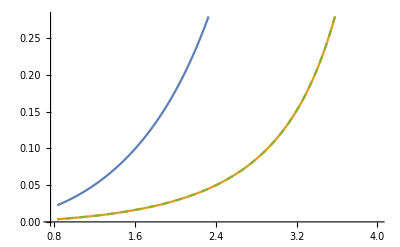

```mathematica
ListLinePlot[{qextDrude1,qextDrude2,Style[qextDrude3,Dashed]}]
```